```mathematica
PrependTo[$Path,NotebookDirectory[]];
<< "GaussianPiecewiseIntegrals`"
```

```mathematica
Theta[x]:=Piecewise[{{1,x>0}},0];
```

```mathematica
IntInf[f_,intvar_:x]:=Integrate[f,{intvar,-Infinity,Infinity}]
IntInf[f_,intvar_:x]:=GaussianIntegral[f,intvar]
calcStats[f_,H_]:=Module[{fl2=f/Sqrt[IntInf[f^2]]},{N[IntInf[fl2*H[fl2]]],N[IntInf[x^2 f]],N[IntInf[x^4 f]]}]
reportStats[f_,H_]:=reportStats[calcStats[f,H]]
ToStringMod[x_]:=If[NumericQ[x]&&Im[x]==0&&x!=0&&Re[Log10[x]]<=-5,ToString[ScientificForm[x],TraditionalForm],ToString[x]]
reportStats[stats_]:="⟨x^2⟩ = "<>ToStringMod[stats[[2]]]<>"\n ⟨x^4⟩ = "<>ToStringMod[stats[[3]]]<>"\n ⟨H⟩ = "<>ToStringMod[stats[[1]]];
reportStatsComparison[stats_,comparison_]:=Module[{del={stats[[1]],stats[[2]]-comparison[[2]],stats[[3]]-comparison[[3]]}},"Δ⟨x^2⟩ = "<>ToStringMod[del[[2]]]<>"\nΔ⟨x^4⟩ = "<>ToStringMod[del[[3]]]<>"\n⟨H⟩ = "<>ToStringMod[del[[1]]]]
reportStatsComparison[f_,H_,comparison_]:=reportStatsComparison[calcStats[f,H],comparison]
Opsubs[Op_,subs_]:=(Op[#]/.subs)&
```

```mathematica
$Assumptions={a>0&&a∈Reals&&c∈Reals&&c>0&&Γ∈Reals&&Γ>0&&d∈Reals&&d>0&&x∈Reals&&t∈Reals&&t>0&&x0>0}
```

{a>0&&a∈ℝ&&c∈ℝ&&c>0&&Γ∈ℝ&&Γ>0&&d∈ℝ&&d>0&&x∈ℝ&&t∈ℝ&&t>0&&x0>0}

```mathematica
K[f_]:=(a x-c(1/2-Theta[x]))f+Γ D[f,x];
L[f_]:=D[K[f],x];
Ldag[f_]:=-(a x-c(1/2-Theta[x]))D[f,x]+Γ D[f,{x,2}];
H[f_]:=Simplify[Ldag[L[f]]];
```

```mathematica
(*E P=L[P] steady-state equation*)
geneq=0==K[P[x]];
exact=DSolveValue[geneq,P[x],x];
exactnormed=exact/IntInf[exact]

(*geneq=FullSimplify[En P[x]==L[P[x]]]*)
```

-(ⅇ^(-c^2/(8 a Γ)+(Piecewise[{{(c x-a x^2)/(2 Γ), x≤0}, {-(c x+a x^2)/(2 Γ), True}}])) √(a Γ))/(√(2 π) Γ (-1+Erf[c/(2 √2 √(a Γ))]))

```mathematica
psi=Exp[-d x^2]/Sqrt[IntInf[Exp[-2d x^2]]]
psiL1=psi/IntInf[psi];
```

d^(1/4) ⅇ^(-d x^2) (2/π)^(1/4)

```mathematica
Eresult=FullSimplify[IntInf[psi*H[psi]]]
```

(3 a^2)/4+(c^2 d)/4+a c √d √(2/π)-3 a d Γ+3 d^2 Γ^2

```mathematica
dsol=Last[Refine[Solve[{D[Eresult,d]==0,D[Eresult,{d,2}]>0},d]]]
```

{d→ConditionalExpression[Root[(8 a^2 c^2)/π+(-c^4+24 a c^2 Γ-144 a^2 Γ^2) #1+(-48 c^2 Γ^2+576 a Γ^3) #1^2-576 Γ^4 #1^3&,2], ]}

```mathematica
psifinal=Simplify[psi/.dsol];
psifinalnorm=psiL1/.dsol;
```

```mathematica
params={a->2,c->1,Γ->3};
```

```mathematica
toplot=psifinalnorm/.params;
exactparams=exactnormed/.params;
Hsubs=Opsubs[H,params];
exactstats=calcStats[exactparams,Hsubs];
```

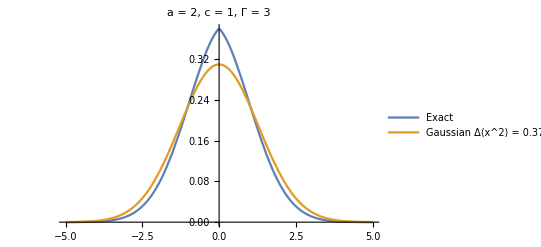

```mathematica
gaussianplot=Plot[{Legended[exactparams,"Exact"],Legended[toplot,"Gaussian\n"<>reportStatsComparison[toplot, Opsubs[H,params],exactstats]]},{x,-5,5},PlotRange->Full,ImageMargins->2,PlotLabel->"a = "<>ToString[a/.params]<>", c = "<>ToString[c/.params]<>", Γ = "<>ToString[Γ/.params]]
```

```mathematica
paramtable=Table[{a->2,c->2i+1,Γ->2j+1},{i,0,0},{j,0,0}]
func=Show[{Plot[{exactnormed/.#,psifinalnorm/.#},{x,-5,5},PlotRange->Full,PlotLabel->"c = "<>ToString[c/.#]<>", Γ = "<>ToString[Γ/.#]],Graphics[Style[Text["(a)",Scaled[{0.1,0.9}]],FontSize->15]]},ImageSize->All]&;
plotsoutputgaussian=EchoTiming[GraphicsGrid[Map[func,paramtable,{2}],ImageSize->300*Length[paramtable],Spacings->Scaled[0.01],ImageMargins->15]]
```

{{{a→2,c→1,Γ→1}}}

1.73532

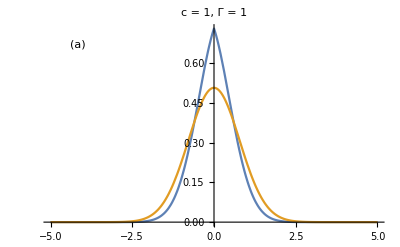

```mathematica
Export[NotebookDirectory[]<>"Images\\Variational Theta Gaussian.png",plotsoutputgaussian,"PNG"]
```

```mathematica
psi2unnormed=(Piecewise[{{ⅇ^(-1/2 d (x0+x)^2), x>0}, {ⅇ^(-1/2 d (-x0+x)^2), True}}]);
psi2=psi2unnormed/Sqrt[IntInf[psi2unnormed^2]]
psi2L1=psi2unnormed/IntInf[psi2unnormed];
```

Piecewise[{{ⅇ^(-1/2 d (x+x0)^2), x>0}, {ⅇ^(-1/2 d (x-x0)^2), True}}]/(π^(1/4) √(-(-1+Erf[√d x0])/(√d)))

```mathematica
Eresult2=IntInf[psi2*H[psi2]];
```

```mathematica
(*iterativeMinimize[Eresult_,dsol_,steps_]:=Module[{intermediateE=Eresult,x0sol,dsolintermediate},
dsolintermediate=dsol;
For[i=0,i<steps,i++,
intermediateE=Eresult/.dsolintermediate;
x0sol=NMinimize[{intermediateE,intermediateE>=0},{{x0,0,10}},Method->"RandomSearch",MaxIterations->200][[2]];
intermediateE=Eresult/.x0sol;
dsolintermediate=NMinimize[{intermediateE,intermediateE>=0},{{d,0,10}},Method->"RandomSearch"][[2]];
];
Join[dsolintermediate,x0sol]
]*)
MinimizeEresult2[params_]:=NMinimize[{Eresult2/.params,x0>=0,d>0,Eresult2>=0/.params},{x0,d}]
```

```mathematica
numij=2;
paramtable=Table[{graphic->Graphics[Style[Text["("<>(Alphabet[][[numij*i+j+1]])<>")",Scaled[{0.1,0.9}]],FontSize->15]],a->2,c->2i+1,Γ->2j+1},{i,0,numij},{j,0,numij}];
func2[params_]:=Module[{psi,dsolparams,Eresultparams,sol,Hsubs,gaussianstats,psistats},
dsolparams=dsol/.params;
Eresultparams=Eresult2/.params;
sol=MinimizeEresult2[params][[2]];
psi=psi2L1/.sol/.params;
Hsubs=Opsubs[H,params];
gaussianstats=If[(psifinalnorm/.params)===Undefined,": no fit","\n"<>reportStatsComparison[psifinalnorm/.params,Hsubs,exactstats]];
psistats=If[psi===0.0,": no fit","\n"<>reportStatsComparison[psi,Hsubs,exactstats]];
Show[{Plot[{exactnormed/.params,psifinalnorm/.params,psi},{x,-5,5},PlotLegends->{"Exact","Gaussian"<>gaussianstats,"Piecewise"<>psistats},PlotRange->Full,PlotLabel->"c = "<>ToString[c/.params]<>", Γ = "<>ToString[Γ/.params]],graphic/.params},ImageSize->All]
];
plotsoutput=EchoTiming[GraphicsGrid[Map[func2,paramtable,{2}],ImageSize->340*Length[paramtable],Spacings->Scaled[0.01],ImageMargins->20]]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

12.3451

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"Images\\Variational Theta.png",plotsoutput,"PNG"]
```

C:\Users\ethan\OneDrive\Documents\Wolfram Mathematica\Final versions for thesis\Images\Variational Theta.png

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

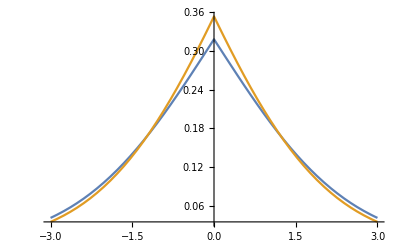

```mathematica
tempparams={a->2,c->9,Γ->11};
tempsol=MinimizeEresult2[tempparams][[2]];
(*reportStatsComparison[psi2L1/.tempparams/.tempsol,Opsubs[H,tempparams],exactstats]*)
Plot[{exactnormed/.tempparams,psi2L1/.tempparams/.tempsol},{x,-3,3},PlotRange->Full]
```